# Astroproyecto – Variabilidad

Amado Cabrera, Marcelo Lam y Mariana Pérez

## Datos recopilados y generados

```mathematica
data=Import[NotebookDirectory[]<>"browse_results.csv","Dataset","HeaderLines"->1]
```

```mathematica
datobj=data[1;;5]
```

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/datos-objetivo.pdf",datobj]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/datos-objetivo.pdf

```mathematica
results=Import[NotebookDirectory[]<>"results.csv","Dataset","HeaderLines"->1]
```

```mathematica
datgen=results[1;;5,{"Name","Fractional Variability","Fractional Variability Error"}]
```

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/datos-generados.pdf",datgen]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/datos-generados.pdf

## Variabilidad fraccionaria contra Flujo

### Variabilidad frac vs Flujo (Objetivo)

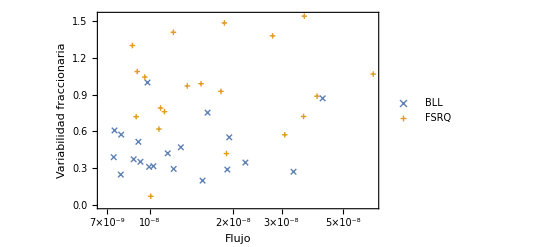

```mathematica
plotobj=ListPlot[{
(List@@#)&/@Normal[data[Select[#[[6]]=="bll"&],{"flux_1_100_gev","frac_variability"}]],(List@@#)&/@Normal[data[Select[#[[6]]=="fsrq"&],{"flux_1_100_gev","frac_variability"}]]
},
Frame->True,
FrameLabel->{"Flujo","Variabilidad fraccionaria"},
PlotMarkers->(Style[#,Magnification->1.5]&/@{"×","+"}),
ScalingFunctions->{"Log",None},
PlotLegends->{"BLL","FSRQ"}
]
```

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/plot-objetivo.pdf",plotobj]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/plot-objetivo.pdf

### Variabilidad frac vs Flujo (Calculado)

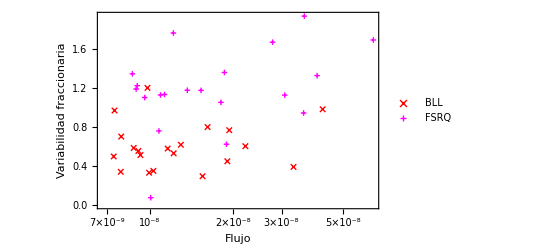

```mathematica
plotcalc=ListPlot[{
Table[
{
data[Select[#[[1]]==blazar&],"flux_1_100_gev"][[1]],
results[Select[#[[1]]==blazar&],"Fractional Variability"][[1]]
},{blazar,Normal[data[Select[#[[6]]=="bll"&],"name"]]}
],
Table[
{
data[Select[#[[1]]==blazar&],"flux_1_100_gev"][[1]],
results[Select[#[[1]]==blazar&],"Fractional Variability"][[1]]
},{blazar,Normal[data[Select[#[[6]]=="fsrq"&],"name"]]}
]
},
Frame->True,
FrameLabel->{"Flujo","Variabilidad fraccionaria"},
PlotMarkers->(Style[#,Magnification->1.5]&/@{"×","+"}),
ScalingFunctions->{"Log",None},
PlotStyle->{Red,Magenta},
PlotLegends->{"BLL","FSRQ"}
]
```

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/plot-generados.pdf",plotcalc]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/plot-generados.pdf

## Comparativa de valores

### Comparativa de valores (Video)

```mathematica
uncertain=Table[
ListPlot[
{
Around[
data[Select[#[[1]]==blazar&],"frac_variability"][[1]],
data[Select[#[[1]]==blazar&],"frac_variability_error"][[1]]
],
Around[
results[Select[#[[1]]==blazar&],"Fractional Variability"][[1]],
results[Select[#[[1]]==blazar&],"Fractional Variability Error"][[1]]
]
},
Frame->True,
FrameLabel->{None,"Variabilidad fraccionaria"},
PlotLabel->blazar<>" ("<>ToUpperCase[data[Select[#[[1]]==blazar&],"source_type"][[1]]]<>")",
PlotStyle->If[data[Select[#[[1]]==blazar&],"source_type"][[1]]=="bll",Orange,Blue],
PlotRange->{{0,3},All}
],{blazar,Normal[data[All,"name"]]}
];
```

```mathematica
ListAnimate[uncertain]
```

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/plot-uncertain3.pdf",uncertain[[13]]]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/plot-uncertain3.pdf

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/plot-uncertain3.pdf",uncertain[[23]]]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/plot-uncertain3.pdf

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/plot-uncertain3.pdf",uncertain[[1]]]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/plot-uncertain3.pdf

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/anim-uncertain.gif",uncertain,
"DisplayDurations"->ConstantArray[0.75,40]
]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/anim-uncertain.gif

```mathematica
i=0
Do[
i++;
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/"<>ToUpperCase[data[Select[#[[1]]==blazar&],"source_type"][[1]]]<>"/"<>blazar<>".pdf",uncertain[[i]]],
{blazar,Normal[data[All,"name"]]}
]
```

0

### Comparativa de valores (Resumen)

Cantidad de blazares que entran en la incerteza del objetivo

```mathematica
CountsBy[
Table[
IntervalIntersection@@{
Around[
data[Select[#[[1]]==blazar&],"frac_variability"][[1]],
data[Select[#[[1]]==blazar&],"frac_variability_error"][[1]]
]["Interval"],
Around[
results[Select[#[[1]]==blazar&],"Fractional Variability"][[1]],
results[Select[#[[1]]==blazar&],"Fractional Variability Error"][[1]]
]["Interval"]
},{blazar,Normal[data[All,"name"]]}
],
Interval[]=!=#&
]
```

<|True→14,False→26|>

Desglose por BLL

```mathematica
CountsBy[
Table[
IntervalIntersection@@{
Around[
data[Select[#[[1]]==blazar&],"frac_variability"][[1]],
data[Select[#[[1]]==blazar&],"frac_variability_error"][[1]]
]["Interval"],
Around[
results[Select[#[[1]]==blazar&],"Fractional Variability"][[1]],
results[Select[#[[1]]==blazar&],"Fractional Variability Error"][[1]]
]["Interval"]
},{blazar,Normal[data[Select[#[[6]]=="bll"&],"name"]]}
],
Interval[]=!=#&
]
```

<|True→7,False→13|>

y FSRQ

```mathematica
CountsBy[
Table[
IntervalIntersection@@{
Around[
data[Select[#[[1]]==blazar&],"frac_variability"][[1]],
data[Select[#[[1]]==blazar&],"frac_variability_error"][[1]]
]["Interval"],
Around[
results[Select[#[[1]]==blazar&],"Fractional Variability"][[1]],
results[Select[#[[1]]==blazar&],"Fractional Variability Error"][[1]]
]["Interval"]
},{blazar,Normal[data[Select[#[[6]]=="fsrq"&],"name"]]}
],
Interval[]=!=#&
]
```

<|False→13,True→7|>

## Histograma de variabilidades fraccionarias

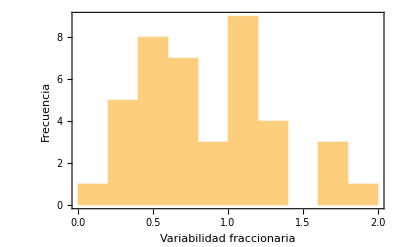

```mathematica
hist=Histogram[results[All,"Fractional Variability"]//Normal,7,
Frame->True,
FrameLabel->{"Variabilidad fraccionaria","Frecuencia"}
]
```

```mathematica
Export["/home/amadoc/Desktop/Projects/Astro/Resultados/histograma.pdf",hist]
```

/home/amadoc/Desktop/Projects/Astro/Resultados/histograma.pdf